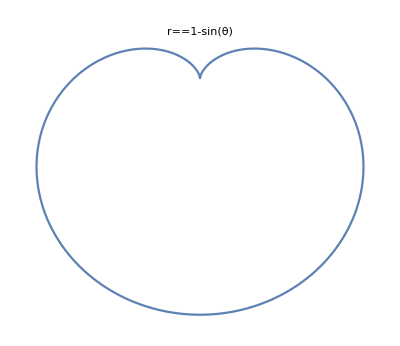

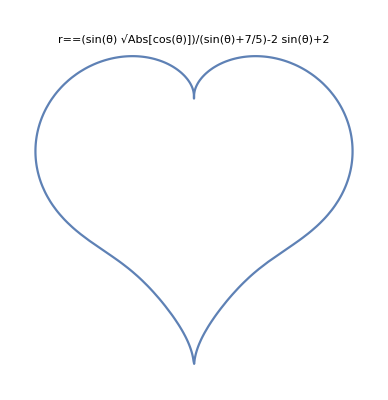

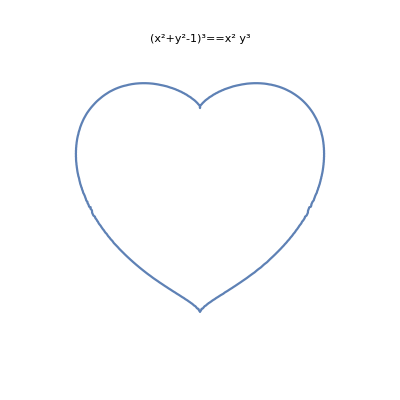

```mathematica
fuc=FromPolarCoordinates[{1-Sin[θ],θ}];
ParametricPlot[fuc,{θ,0,2Pi},Axes->False,PlotLabel->r==1-Sin[θ]]
fuc=FromPolarCoordinates[{Sin[θ]Sqrt[Abs[Cos[θ]]]/(Sin[θ]+7/5)-2Sin[θ]+2,θ}];
ParametricPlot[fuc,{θ,0,2Pi},Axes->False,PlotLabel->r==TraditionalForm[Sin[θ]Sqrt[Abs[Cos[θ]]]/(Sin[θ]+7/5)-2Sin[θ]+2]]
ContourPlot[{(x^2+y^2-1)^3==x^2*y^3},{x,-1.5,1.5},{y,-1.5,1.5},Frame->False,PlotLabel->TraditionalForm[(x^2+y^2-1)^3==x^2*y^3]]
```

```mathematica
Manipulate[RegionPlot3D[ ( x^2/a^2+y^2+z^2<1&&x>=y) ||(x^2+ y^2/a^2+z^2<1&&x<=y),{x,-2,2},{y,-2,2},{z,-2,2},ViewPoint->{0,0,10},ViewVertical->{1,1,0},Mesh->None,PlotPoints->35,PerformanceGoal->"Speed",Boxed->False,Axes->False,PlotStyle->Directive[col,Specularity[White,10]],ImageSize->{480,440}],{{a,1.7,"semiaxis"},1.5,2.,0.05,Appearance->"Labeled"},{{col,Red,"color"},Red}]
```

```mathematica
TableForm@{"▽(⊙·⊙)=⊙▽⊙+⊙▽⊙","d(·ω·d)","(∫·ω·)∫","∂(·ω·∂)","(∮·ω·)∮","∇(·ω·∇)"}
```

▽(⊙·⊙)=⊙▽⊙+⊙▽⊙
d(·ω·d)
(∫·ω·)∫
∂(·ω·∂)
(∮·ω·)∮
∇(·ω·∇)

```mathematica
字体
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
ContourPlot3D[(x^2+(9/4)y^2+z^2-1)^3-x^2z^3-(9/80)y^2z^3==0,{x,-2,2},{y,-2,2},{z,-2,2},Axes->False,Boxed->False]
```

-Graphics3D-